## Initializing truncated theta functions (run first)

```mathematica
Clear[d,x,k,j]
thetaest[x_,d_,j_]:=1+2Sum[Exp[-d k^2]Cos[2Pi k x],{k,j}];
thetaestt[t_,d_,j_]:=1+2Sum[Exp[-d k^2]Cos[k ArcCos[t]],{k,j}];
thetaestprime[x_,d_,j_]:=-2Sum[2Pi k Exp[-d k^2]Sin[2Pi k x],{k,j}];
thetaesttprime[t_,d_,j_]:=2Sum[ k Exp[-d k^2]Sin[k ArcCos[t]]/Sqrt[1-t^2],{k,j}];
thetaesttprime[1,d_,j_]:=2Sum[k^2Exp[-d k^2],{k,j}];
thetaesttprime[-1,d_,j_]:=2Sum[k^2Exp[-d k^2](-1)^(k+1),{k,j}];
points={1,0,-1};
lowhigh={-1,1};
```

## Basic Value and Derivative Bounds, small a (run second)

### Small a

Here we encode the bounds on theta functions when the theta parameter a is at most Pi^2, see appendix section A. The first argument is 0,1, or 2 depending on whether we are considering value, first derivative, or second derivative, the second argument is the t value at which we are evaluating, and the third argument is -1 for a lower bound, 1 for an upper bound .

First the value bounds:

```mathematica
Clear[f1,f2,c]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f1[0,points[[j]],lowhigh[[i]]]=thetaestt[points[[j]],d,2]+lowhigh[[i]]*Exp[-4d]/50]]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f2[0,points[[j]],lowhigh[[i]]]=thetaestt[points[[j]],c,2]+lowhigh[[i]]*Exp[-4c]/50]]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f1[1,points[[j]],lowhigh[[i]]]=thetaesttprime[points[[j]],d,2]+lowhigh[[i]]*Exp[-4d]/8]]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f2[1,points[[j]],lowhigh[[i]]]=thetaesttprime[points[[j]],c,2]+lowhigh[[i]]*Exp[-4c]/8]]
```

```mathematica
f1[0,-1,-1]//Expand
f1[0,-1,1]//Expand
f1[0,0,-1]//Expand
f1[0,0,1]//Expand
f1[0,1,-1]//Expand
f1[0,1,1]//Expand
f1[1,-1,-1]//Expand
f1[1,-1,1]//Expand
f1[1,0,-1]//Expand
f1[1,0,1]//Expand
f1[1,1,-1]//Expand
f1[1,1,1]//Expand
```

1+(99 ⅇ^(-4 d))/50-2 ⅇ^-d

1+(101 ⅇ^(-4 d))/50-2 ⅇ^-d

1-(101 ⅇ^(-4 d))/50

1-(99 ⅇ^(-4 d))/50

1+(99 ⅇ^(-4 d))/50+2 ⅇ^-d

1+(101 ⅇ^(-4 d))/50+2 ⅇ^-d

-65/8 ⅇ^(-4 d)+2 ⅇ^-d

-63/8 ⅇ^(-4 d)+2 ⅇ^-d

-1/8 ⅇ^(-4 d)+2 ⅇ^-d

ⅇ^(-4 d)/8+2 ⅇ^-d

(63 ⅇ^(-4 d))/8+2 ⅇ^-d

(65 ⅇ^(-4 d))/8+2 ⅇ^-d

### Large a

Here we encode the bounds on theta functions when the theta parameter a is at least Pi^2, see appendix section A.The first argument is 0 or 1 depending on whether we are considering value or first derivative, the second argument is the t value at which we are evaluating, and the third argument is - 1 for a lower bound, 1 for an upper bound . e will play the role of epsilon, e2 of epsilon_2,  e3 of epsilon_3.

```mathematica
Clear[e,e2,e3]
```

```mathematica
Lf1[0,-1,-1]=2Exp[-a/4];
Lf1[0,-1,1]=2(1+e)Exp[-a/4];
Lf1[0,0,-1]=Exp[-a/16];
Lf1[0,0,1]=Exp[-a/16](1+e2);
Lf1[0,1,-1]=1;
Lf1[0,1,1]=1+e;
Lf1[1,-1,-1]=a/(2Pi^2)(a-2)Exp[-a/4];
Lf1[1,-1,1]=a/(2Pi^2)(a-2+e)Exp[-a/4];
Lf1[1,0,-1]=a(1-e3)/(4Pi)Exp[-a/16];
Lf1[1,0,1]=a/(4Pi)Exp[-a/16];
Lf1[1,1,-1]=(1-e2)a/(2Pi^2);
Lf1[1,1,1]=a/(2Pi^2);
```

```mathematica
Lf2[0,-1,-1]=2Exp[-b/4];
Lf2[0,-1,1]=2(1+e)Exp[-b/4];
Lf2[0,0,-1]=Exp[-b/16];
Lf2[0,0,1]=Exp[-b/16](1+e2);
Lf2[0,1,-1]=1;
Lf2[0,1,1]=1+e;
Lf2[1,-1,-1]=b/(2Pi^2)(b-2)Exp[-b/4];
Lf2[1,-1,1]=b/(2Pi^2)(b-2+e)Exp[-b/4];
Lf2[1,0,-1]=b(1-e3)/(4Pi)Exp[-b/16];
Lf2[1,0,1]=b/(4Pi)Exp[-b/16];
Lf2[1,1,-1]=(1-e2)b/(2Pi^2);
Lf2[1,1,1]=b/(2Pi^2);
```

## Monotonicity of the Bounds in Lemmas 10, 11, 12

In each of lemmas 10,11, 12, we produce bounds on certain quantities involving the theta function, which we claim are monotone in the gaussian parameter. The proofs of these claims are straightforward but included here for completeness:

#### Lemma 10

Note that our upper bound for (2 f1’ (1) - f1 (1)) is positive for a1>=pi^2, yielding the following upper bound for (2 f1' (1) - f1 (1))/f1 (-1) :

```mathematica
(2Lf1[1,1,1]-Lf1[0,1,-1])/.{a->a1}
(2Lf1[1,1,1]-Lf1[0,1,-1])/Lf1[0,-1,-1]/.{a->a1}//Simplify
```

-1+a1/π^2

1/2 ⅇ^(a1/4) (-1+a1/π^2)

This is certainly increasing in a1 for a1>= pi^2

Now note the term f2' (0) - f2 (0) is bounded below by :

```mathematica
(Lf2[1, 0, -1] - Lf2[0, 0, 1])/. {b->a2,e2 -> 1/50, e3 -> 1/40} // Simplify
```

-(3 ⅇ^(-a2/16) (-65 a2+272 π))/(800 π)

and this quantity is nonnegative iff a2 >= 272 pi/65. Thus,  for a2>=272pi/65, we have the following lower bound of (f2' (0) - f2 (0))/f2 (-1) :

```mathematica
(Lf2[1,0,-1]-Lf2[0,0,1])/Lf2[0,-1,1]/.{b->a2,e->1/1000,e2->1/50,e3->1/40}//Simplify
```

-(15 ⅇ^(3 a2/16) (-65 a2+272 π))/(8008 π)

If Pi^2 < a2 < 272 Pi/65, we have the following, slightly different lower bound of (f2' (0) - f2 (0))/f2 (-1) :

```mathematica
(Lf2[1,0,-1]-Lf2[0,0,1])/Lf2[0,-1,-1]//.{b->a2,e->1/1000,e2->1/50,e3->1/40}//Simplify
```

-(3 ⅇ^(3 a2/16) (-65 a2+272 π))/(1600 π)

Note these two bounds are equal up to a positive constant factor. We differentiate -ⅇ^(3 a2/16) (-1040-195 a2+816 π)to show these bounds are increasing in a2:

```mathematica
D[-ⅇ^(3 a2/16) (-65 a2+272 π),a2]//Simplify
```

1/16 ⅇ^(3 a2/16) (1040+195 a2-816 π)

for a2 > Pi^2, this is certainly positive, as its sign depends only on  1040 + 195 a2 - 816 pi, which is positive for a2 >= pi^2:

```mathematica
(1040+195 a2-816 π/.a2->Pi^2)>0
```

True

Thus, the bounds are increasing in a2 for a2 >= pi^2, as claimed .

#### Lemma 11

Here is our upper bound for (2 f1' (1) - f1 (1)) when a1 <= pi^2 (i . e . d 1>= 1).  Note this bound is decreasing in d1, and so it suffices to check its negativity at d1=1 to show it is negative for all d1>=1

```mathematica
(2 f1[1, 1, 1] - f1[0, 1, -1])/.{d->d1}//Expand
((2 f1[1, 1, 1] - f1[0, 1, -1])/.d->1)<0
```

-1+(1427 ⅇ^(-4 d1))/100+2 ⅇ^-d1

True

Thus, we obtain the following upper bound for (2 f1' (1) - f1 (1))/f1 (-1) :

```mathematica
(2 f1[1, 1, 1] - f1[0, 1, -1])/f1[0, -1,1]/.d->d1
```

(-1+ⅇ^(-4 d1)/50-2 (ⅇ^(-4 d1)+ⅇ^-d1)+2 (ⅇ^(-4 d1)/8+2 (4 ⅇ^(-4 d1)+ⅇ^-d1)))/(1+ⅇ^(-4 d1)/50+2 (ⅇ^(-4 d1)-ⅇ^-d1))

To show it is increasing in a1, we show it is decreasing in d1 . Via the quotient rule, the sign of the derivative with respect to d1 depends only on the sign of:

```mathematica
D[(2 f1[1, 1, 1] - f1[0, 1, -1]),d]f1[0, -1,1] -(2 f1[1, 1, 1] - f1[0, 1, -1])D[f1[0, -1, 1],d]/.{d->d1}//Expand
```

(4887 ⅇ^(-5 d1))/50-(1629 ⅇ^(-4 d1))/25

By Lemma 40 of 13, this quantity is negative for all d1>=1 if and only if it is negative for d=1.

```mathematica
((4887 ⅇ^(-5 d1))/50-(1629 ⅇ^(-4 d1))/25/.d1->1)<0
```

True

Thus, our upper bound for (2 f1' (1) - f1 (1))/f1 (-1) is decreasing for d1 >= 1, or equivalently, increasing for 0 < a1 <= pi^2, as desired.

Similarly, we have the lower bound for f2’(0)-f2(0) whose negativity for d2>=1 is verified by checking at d2=1 and invoking Lemma 40:

```mathematica
( f2[1,0, -1] - f2[0, 0,1])/.{c->d2}//Expand
(( f2[1,0, -1] - f2[0, 0,1])/.{c->1})<0
```

-1+(371 ⅇ^(-4 d2))/200+2 ⅇ^-d2

True

Thus, we have the following lower bound for (f2' (0) - f2 (0))/f2 (-1) and its derivative with respect to d2 depends only on the sign of the next term:

```mathematica
( f2[1,0, -1] - f2[0, 0,1])/f2[0,-1,-1]/.{c->d2}
D[( f2[1,0, -1] - f2[0, 0,1]),c]f2[0,-1,-1]-D[f2[0,-1,-1],c]( f2[1,0, -1] - f2[0, 0,1])/.{c->d2}//Expand
```

(-1+(371 ⅇ^(-4 d2))/200+2 ⅇ^-d2)/(1-ⅇ^(-4 d2)/50+2 (ⅇ^(-4 d2)-ⅇ^-d2))

(2301 ⅇ^(-5 d2))/100-(767 ⅇ^(-4 d2))/50

Again by Lemma 40, the sign of (2301 ⅇ^(-5 d2))/100-(767 ⅇ^(-4 d2))/50 for all d2>=1 is determined by the sign when d2=1. which we check:

```mathematica
((2301 ⅇ^(-5 d2))/100-(767 ⅇ^(-4 d2))/50/.d2->1)<0
```

True

Thus, our lower bound for (f2' (0) - f2 (0))/f2 (-1) is decreasing for d2 >= 1, or equivalently, increasing for 0 < a2 <= pi^2, as desired .

#### Lemma 12

Our large a1 and a2 upper and lower bounds are:

```mathematica
Lf1[1,-1,-1]/Lf1[1,1,1]/.{a->a1}
Lf2[0,-1,1]/Lf2[0,1,-1]/.{b->a2,e->1/1000}
```

(-2+a1) ⅇ^(-a1/4)

(1001 ⅇ^(-a2/4))/500

The second bound is clearly decreasing in a2, and the first bound is decreasing for a1 >= pi^2 as seen by calculating the derivative below ...

```mathematica
D[(a1-2)Exp[-a1/4],a1]//Simplify
```

-1/4 (-6+a1) ⅇ^(-a1/4)

Our small a1 and a2 bounds are:

```mathematica
f1[1,-1,-1]/f1[1,1,1]/.{d->d1}
f2[0,-1,1]/f2[0,1,-1]/.{c->d2}
```

(-1/8 ⅇ^(-4 d1)+2 (-4 ⅇ^(-4 d1)+ⅇ^-d1))/(ⅇ^(-4 d1)/8+2 (4 ⅇ^(-4 d1)+ⅇ^-d1))

(1+ⅇ^(-4 d2)/50+2 (ⅇ^(-4 d2)-ⅇ^-d2))/(1-ⅇ^(-4 d2)/50+2 (ⅇ^(-4 d2)+ⅇ^-d2))

and their derivatives' (with respect to d1 and d2) sign depend only on the signs of:

```mathematica
D[f1[1,-1,-1],d]f1[1,1,1]-f1[1,-1,-1]D[f1[1,1,1],d]/.{d->d1}//Expand
D[f2[0,-1,1],c]f2[0,1,-1]-f2[0,-1,1]D[f2[0,1,-1],c]/.{c->d2}//Expand
```

(195 ⅇ^(-5 d1))/2

-24 ⅇ^(-5 d2)-(4 ⅇ^(-4 d2))/25+4 ⅇ^-d2

The first of these is clearly positive for all d1>=1, and the second is positive for all d2 >= 1 by checking at d2 = 1 (see below) and invoking Lemma 40. Thus, the bounds are increasing in d1 and d2, and so decreasing in a1 and a2, as desired.

```mathematica
(D[f2[0,-1,1],c]f2[0,1,-1]-f2[0,-1,1]D[f2[0,1,-1],c]/.{c->d2}/.{d2->1})>0
```

True

## Positivity of b02

#### a1>=Pi^2

For this interval, the final inequality we need to verify is the positivity of the below term for a1 >= pi^2 :

```mathematica
(Lf2[1,0,-1]-Lf2[0,0,1])/Lf2[0,-1,1]-(2Lf1[1,1,1]-Lf1[0,1,-1])/Lf1[0,-1,-1]/.{b->4a1/3,a->a1,e->1/1000,e2->1/50,e3->1/40}//Simplify
```

(ⅇ^(a1/4) (-19 π^2+13 a1 (-77+25 π)))/(2002 π^2)

Its sign depends only on (-19 π^2+13 a1 (-77+25 π)) which is increasing in a1 (since 25pi>77), and we check that is positive at a1=pi^2

```mathematica
((-19 π^2+13 a1 (-77+25 π))/.a1->Pi^2)>0
```

True

#### a1 <= Pi^2 and a2>=Pi^2

if a2 >= 272 Pi/65, we just need to use the fact that a2 >= pi^2 to check the positivity of the following :

```mathematica
(-(2 f1[1, 1, 1] - f1[0, 1, -1])/f1[0, -1,1]/.{d->1})>0
```

True

If a2 is in [pi^2,272pi/65], we have to show the difference of two increasing functions, h2-h1, is positive  on the interval [Pi^2, 272Pi/65] . Our maps are :

```mathematica
h2[a2_]:=(Lf2[1,0,-1]-Lf2[0,0,1])/Lf2[0,-1,-1]/.{b->a2,e->1/1000,e2->1/50,e3->1/40}
h1[a2_]:=(2 f1[1, 1, 1] - f1[0, 1, -1])/f1[0, -1,1]/.{d->4Pi^2/(3a2)}
```

Just to provide a visual:

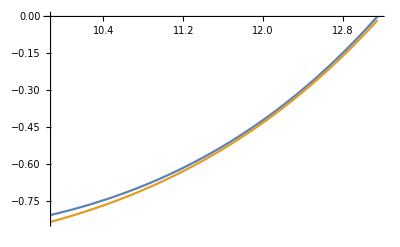

```mathematica
Plot[{h2[a],h1[a]},{a,Pi^2,272Pi/65}]
```

We check the inequality rigorously with the SegmentCheck module, which splits our interval into subintervals evaluates h2 at left endpoints and h1 at right endpoints :

```mathematica
SegmentCheck[h1_,h2_,{a_,b_,n_}]:=Apply[And,Table[h2[a+k*(b-a)/n]>h1[a+(k+1)*(b-a)/n],{k,0,n-1}]]
```

```mathematica
SegmentCheck[h1,h2,{Pi^2,272Pi/65,150}]
```

True

As suggested by the plot, we need a fair number of intervals. Indeed, 100 intervals is not sufficient, though 150 works .

#### a2<=Pi^2

Our final inequality to be shown is :

```mathematica
(f2[1,0, -1] - f2[0, 0,1])f1[0, -1,1]-(2 f1[1, 1, 1] - f1[0, 1, -1])f2[0,-1,-1]/.{c->d2,d->4d2/3}//Expand
```

-9803/400 ⅇ^(-28 d2/3)+1629/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200

By lemma 40 and the check below for d2=1, we have the positivity of -9803/400 ⅇ^(-28 d2/3)+2 ⅇ^(-19 d2/3) for all d2>=1.

```mathematica
(-9803/400 ⅇ^(-28 d2/3)+2 ⅇ^(-19 d2/3)/.d2->1)>0
```

True

Thus, it remains to check the positivity of the below for all d2>=1, or equivalently, we multiply through by e^{16d2/3}, and show the resulting quantity is increasing in d2. Since it is convex in d2, we just take the derivative and evaluate at d2=1.

```mathematica
1529/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200
Exp[16d2/3](1529/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200)//Expand
D[Exp[16d2/3](1529/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200),d2]//Expand
(D[Exp[16d2/3](1529/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200),d2]/.d2->1)>0
```

1529/50 ⅇ^(-19 d2/3)-599/25 ⅇ^(-16 d2/3)+(767 ⅇ^(-4 d2))/200

-599/25+(1529 ⅇ^-d2)/50+767/200 ⅇ^(4 d2/3)

-(1529 ⅇ^-d2)/50+767/150 ⅇ^(4 d2/3)

True

## Proof of Lemma 7

The a1 >= pi^2 case needs no computation . For the case where a1 <= Pi^2 and a2 >= Pi^2, we solely need to check the positivity of the below quantity:

```mathematica
f1[1,-1,-1]/f1[1,1,1]-Lf2[0,-1,1]/Lf2[0,1,-1]/.{d->1,b->Pi^2,e->1/1000}
```

(2 (-4/ⅇ^4+1/ⅇ)-1/(8 ⅇ^4))/(2 (4/ⅇ^4+1/ⅇ)+1/(8 ⅇ^4))-1001/500 ⅇ^(-π^2/4)

```mathematica
(f1[1,-1,-1]/f1[1,1,1]-Lf2[0,-1,1]/Lf2[0,1,-1]/.{d->1,b->Pi^2,e->1/1000})>0
```

True

For the small a case, after rearranging terms, we have to show positivity of :

```mathematica
f1[1,-1,-1]f2[0,1,-1]-f1[1,1,1]f2[0,-1,1]/.{c->d2,d->4d2/3}//Expand
```

-65/2 ⅇ^(-28 d2/3)-1633/100 ⅇ^(-16 d2/3)+8 ⅇ^(-7 d2/3)

By lemma 40, we just need to check the positivity of this quantity at d2 = 1 :

```mathematica
(f1[1,-1,-1]f2[0,1,-1]-f1[1,1,1]f2[0,-1,1]/.{c->d2,d->4d2/3}/.{d2->1})>0
```

True